## Lab 1

Compute both exact and numerical value for each of the following expressions.

(10^2-4(11-5)^3)/(5^6-6^5)

```mathematica
(10^2-4(11-5)^3)/(5^6-6^5)
```

-764/7849

```mathematica
N[-764/7849]
```

-0.0973372

ln 25^3/7^2

```mathematica
Log[25^3/7^2]
```

Log[15625/49]

```mathematica
N[Log[15625/49]]
```

5.76481

log (133/5)

```mathematica
Log10[133/5]
```

Log[133/5]/Log[10]

```mathematica
N[Log[133/5]/Log[10]]
```

1.42488

Apply Simplify to each of the following expressions.

ln (8/E^3)

```mathematica
Simplify[Log[8/E^3]]
```

-3+Log[8]

1/2(1-cos 2x)

```mathematica
Simplify[1/2(1-Cos[2x])]
```

Sin[x]^2

cos^2 2x+sin^2 2x

```mathematica
Simplify[Cos[2x]^2+Sin[2x]^2]
```

1

Factor each polynomial.

2 x^6+6 x^5-36 x^4-56 x^3+240 x^2-256

```mathematica
Factor[2 x^6+6 x^5-36 x^4-56 x^3+240 x^2-256]
```

2 (-2+x)^3 (1+x) (4+x)^2

3 x^3+21 x^2-15x-225

```mathematica
Factor[3 x^3+21 x^2-15x-225]
```

3 (-3+x) (5+x)^2

x^2-5x-24

```mathematica
Factor[x^2-5x-24]
```

(-8+x) (3+x)

Apply Apart to each rational function.

(x^3+3 x^2-5x+1)/(3 x^3+9 x^2-12)

```mathematica
Apart[(x^3+3 x^2-5x+1)/(3 x^3+9 x^2-12)]
```

1/3-5/(3 (2+x)^2)

(x^4-5x+1)/(3 x^3+9 x^2-12)

```mathematica
Apart[(x^4-5x+1)/(3 x^3+9 x^2-12)]
```

-1-1/(9 (-1+x))+x/3-3/(2+x)^2+28/(9 (2+x))

(3 x^2-5x+1)/(3 x^3+9 x^2-12)

```mathematica
Apart[(3 x^2-5x+1)/(3 x^3+9 x^2-12)]
```

-1/(27 (-1+x))-23/(9 (2+x)^2)+28/(27 (2+x))

Plot the graph of f(x)=x^2-5x-24 on the interval [-1,6].

```mathematica
x^2-5x-24
```

-24-5 x+x^2

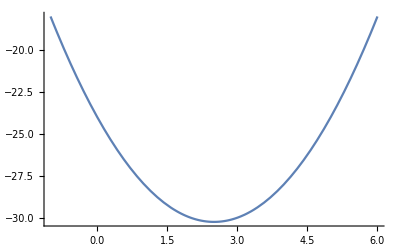

```mathematica
Plot[-24-5 x+x^2,{x,-1, 6}]
```

Plot on one figure the graphs of f(x)=x^2-5x-24,g(x)=5sin x-24, and h(x)=5cos x-24 on the interval [-1,6].

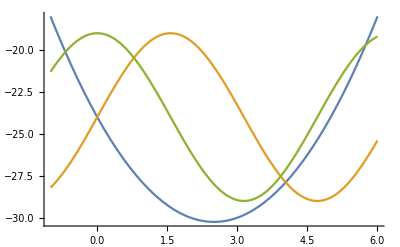

```mathematica
Plot[{x^2-5x-24, 5Sin[x]-24, 5Cos[x]-24}, {x,-1,6}]
```

Find and study related examples for Plot in the Wolfram Documentation, and plot on one figure the graphs of f(x)=x^2-5x-24,g(x)=5sin x-24, and h(x)=5cos x-24 on the interval [-1,6] with the region in between the curves of g(x) and h(x) shaded.

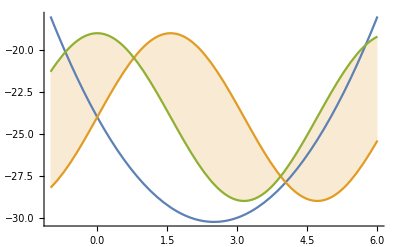

```mathematica
Plot[{x^2-5x-24, 5Sin[x]-24, 5Cos[x]-24}, {x,-1,6}, Filling->{2->{3}}]
```

Do experiment with the following two groups of commands, recognize and explain the difference in their outputs.

x = RandomInteger[{1,25} ];  {x, x, x}

```mathematica
x = RandomInteger[{1,25} ];  {x, x, x}
```

{21,21,21}

```mathematica
{15,15,15}
```

x := RandomInteger[{1,25} ]; {x, x, x}

```mathematica
x := RandomInteger[{1,25} ]; {x, x, x}
```

{5,19,1}

After repeating the output process for these two commands I see that the 8.1 outputs the same number in the set. The number is always between 1 and 25. There is a colon before the equal sign for the 8.2 input. This means 8.2 has an output of a random integer between 1 and 25 as well but the three variables can all be different. For example 8.1 would output {2,2,2} but 8.2 would output {2,3,4}.

Compute the following sums, and make a conjecture about the value of ∑_(i=1)^(10^n) i, where integer n≥1.

∑_(i=1)^10 i

```mathematica
Sum[i, {i,1,10}]
```

55

∑_(i=1)^100 i

```mathematica
Sum[ i, {i,1,100}]
```

5050

∑_(i=1)^1000 i

```mathematica
Sum[i, {i,1,1000}]
```

500500

∑_(i=1)^10000 i

```mathematica
Sum[i, {i,1,10000}]
```

50005000

∑_(i=1)^100000 i

```mathematica
Sum[i, {i,1,100000}]
```

5000050000

The value of ∑_(i=1)^(10^n) i, where integer n≥1 would just continue to increase infinitely. From the outputs we see that there is a pattern. Each summation increases by adding one more zero in between the 5’s. For example ∑_(i=1)^1000000 i  would output the value 500,000,500,000 based on the pattern seen above. This would continue infinitely.